-8 (2+3 x+x^2)

Piecewise[{{-8 (2+3 x+x^2), x≤-1}, {(-3+x) (-1+x^2), -1≤x<3}, {0, True}}]

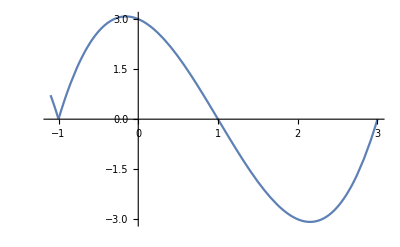

Definitionsbereich:

Reell:True

Komplex:True

Wertebereich:

Reell:y≤16/(3 √3)

Piecewise[{{-8 (3+2 x), x<-1}, {-1-6 x+3 x^2, -1<x<3}, {0, x>3}, {Indeterminate, True}}]

Definitionsbereich:

Reell:x<-1||-1<x<3||x>3

Komplex:x<-1||-1<x<3||x>3

Wertebereich:

Reell:y==0||y>-8||-4≤y<8

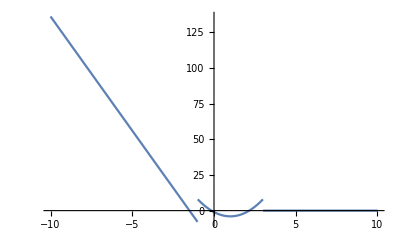

```mathematica
a=-8;
b=5.65;
functionpart1 =a*(-1)^2 * (x^2+3x+2)
definitionsbereich1 = (x≤(-1));
funktionspart2 =(-1)^2 * (x^2-1)*(x-3);
definitionsbereich2 = (-1≤x<3);

func=Piecewise[{{functionpart1, definitionsbereich1},{  funktionspart2,definitionsbereich2}}]
Plot[func,{x,-1.1,3},PlotRange->All]

Print["Definitionsbereich:"]
Print["Reell:",FunctionDomain[func, x, Reals]]
Print["Komplex:",FunctionDomain[func, x, Complexes]]
Print["Wertebereich:"]
Print["Reell:",FunctionRange[func, x, y]]
ableitung = Simplify[D[func,x]]
Print["Definitionsbereich:"]
Print["Reell:",FunctionDomain[ableitung, x, Reals]]
Print["Komplex:",FunctionDomain[ableitung, x, Complexes]]
Print["Wertebereich:"]
Print["Reell:",FunctionRange[ableitung, x, y]]
Plot[ableitung, {x,-10,10}]
```